```mathematica
Manipulate[Plot[f[x],{x,0,2 Pi}],{f,{Sin->Graphics[Disk[]],Cos->"cosine",Tan->"tangent"}}]
```

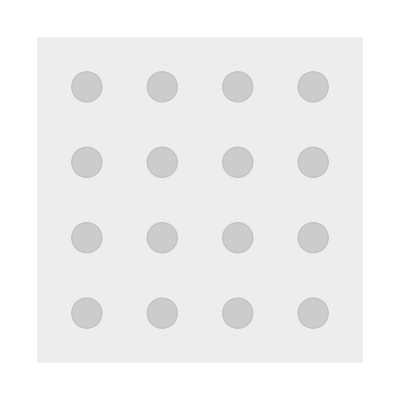

```mathematica
multiwaygraph3[fourcoords, Range[16]/. _Integer->0, fourmoves]
```

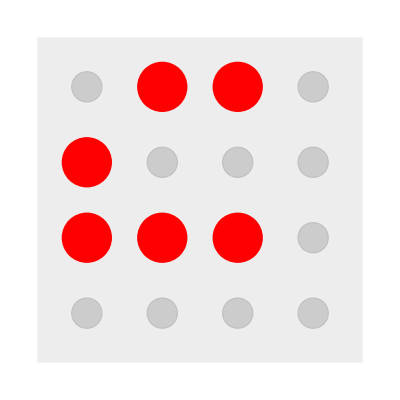
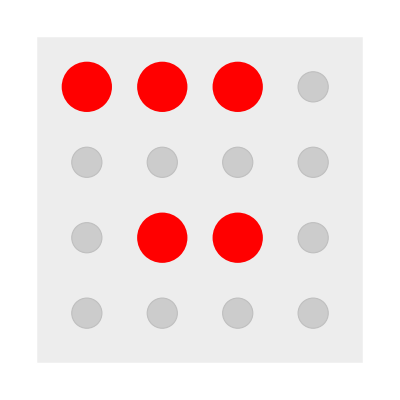
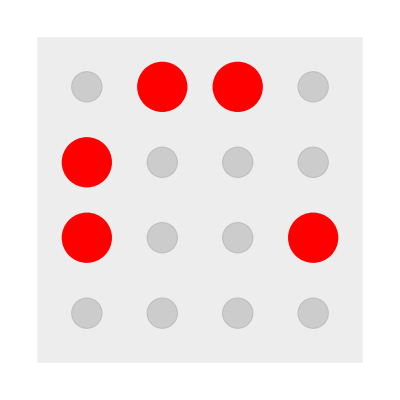
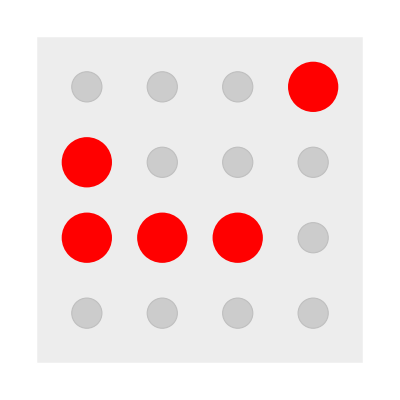
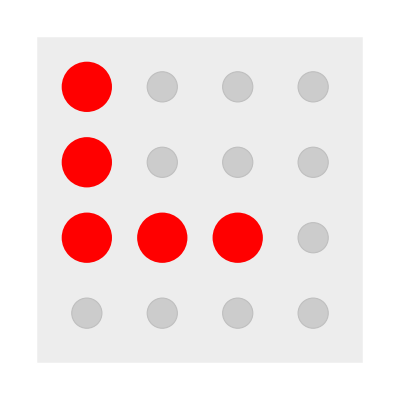
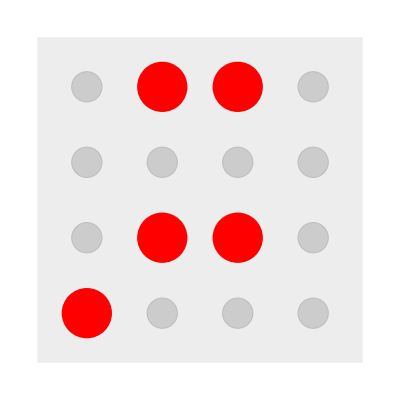
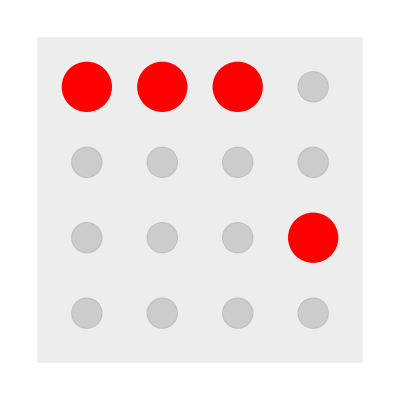
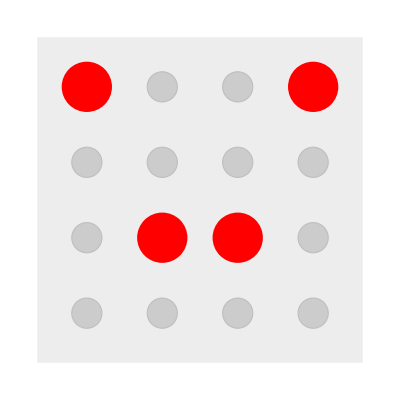
```mathematica
Manipulate[fourFiveGraphHighlight[fivegraph,graph[[1]],graph[[2]][[1]],graph[[2]][[2]],.5,2],{{graph,{multiwaygraph3[fourcoords, Range[16]/. _Integer->0, fourmoves],{1,0}} ," "},{{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,{1,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-][[1]]],{-Graphics-,{1,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]]}}]
```

```mathematica
Partition[Riffle[Table[multiwaygraph3[fourcoords,state,fourmoves],{state, Table[state, {state, Table[getFourCoords[-Graphics-, perm[[1]],perm[[2]]],{perm, options}]}]}],{{1,0},{1,1},{0,1},{0,0}}],2]
```

{{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,{1,0}},{-Graphics-,{1,1}},{-Graphics-,{0,1}},{-Graphics-,{0,0}}}

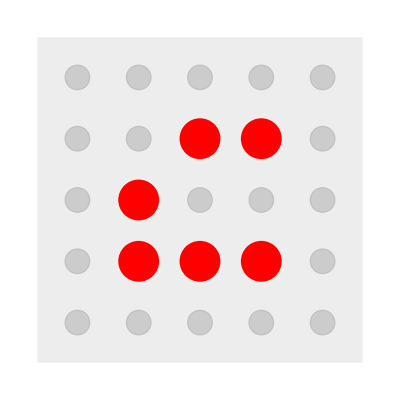
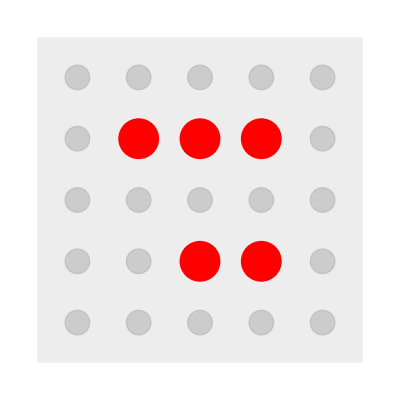
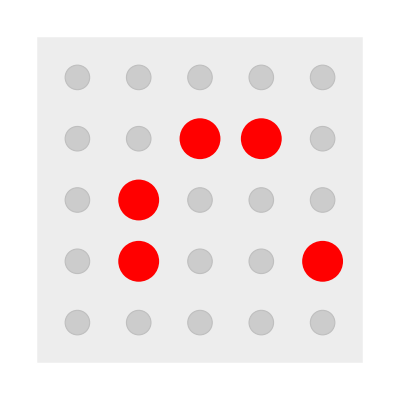
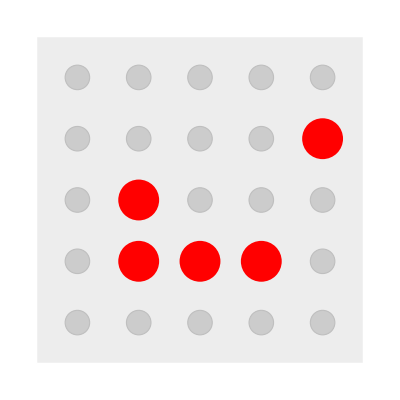
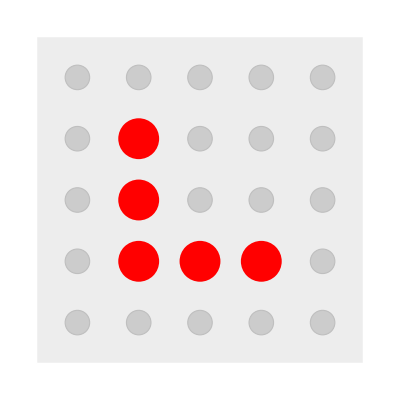
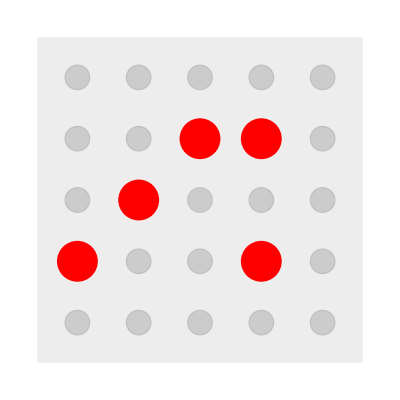
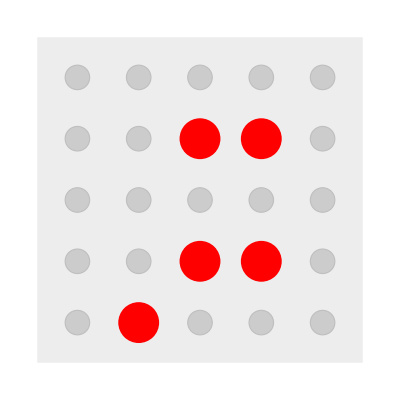
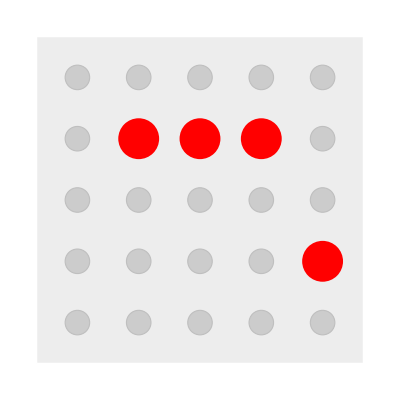
{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[fourFiveGraphHighlight[fivegraph,graph[[1]],graph[[2]][[1]],graph[[2]][[2]],.5,2], {graph,Partition[Riffle[Table[multiwaygraph3[fourcoords,state,fourmoves],{state, Table[state, {state, Table[getFourCoords[-Graphics-, perm[[1]],perm[[2]]],{perm, options}]}]}],{{1,0},{1,1},{0,1},{0,0}}],2]}]
```

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]]
```

-Graphics-

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}]
```

```mathematica
Manipulate[cropGraph[-Graphics-,pins,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}],{pins,9,2,1,Appearance->"Labeled"},ContinuousAction->False]
```

```mathematica
Manipulate[cropGraph2Way[-Graphics-,max,min,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}],{max,9,min+1,1,Appearance->"Labeled"},{min,1,max-1,1,Appearance->"Labeled"}, ContinuousAction->False]
```

```mathematica
cropGraph2Way[-Graphics-,3,2,fourcoords]
```

-Graphics-

```mathematica
%//Timing
```

{0.000103,-Graphics-}

```mathematica
Reverse[Range[5,16]]
```

{16,15,14,13,12,11,10,9,8,7,6,5}

```mathematica
Manipulate[cropGraph2Way[-Graphics-,max,min,fourcoords],{max,4,2,1},{min,2,16,1}]
```

```mathematica
Length[VertexList[-Graphics-][[1]]]
```

16

```mathematica
VertexCount[-Graphics-]
```

513

```mathematica
VertexCount[-Graphics-]
```

10

$Aborted